### Minimierung der Rosebrock-Funktion mittels des Gradientenverfahrens

```mathematica
(* Die Parameter *)
γ=10^(-4);
β=1/2;
ϵ=10^(-3);
```

```mathematica
(* Die Gradientenrichtung und Armijo-Schrittweitenregel *)
AbstiegsRichtung[f_,x_]:=-{D[f[{x01,x02}],x01],D[f[{x01,x02}],x02]}/.{x01->x[[1]],x02->x[[2]]}
ArmijoSchrittweite[f_,x_,s_]:=Module[{σ=1},While[f[x+σ s]-f[x]>σ γ (-AbstiegsRichtung[f,x]).s,σ =σ β];σ]
```

```mathematica
(* An das Verfahren wird eine Testfunktion f, ein Startwert x0, Höchstanzahl an Iterationen n und ein Abbruchbedingung ϵ übergeben. Es berechnet zuerst den Gradientenrichtung s. Diese wird zusätzlich noch in Armijo-Schrittweitenregel benötigt. Zuerst wird getestet, ob die Armijo-Bedingung mit der Schrittweite σ = (β=1/2)^0 = 1 erfüllt ist. Wenn dies nicht zutrifft, wird die Schrittweite so oft mit β=1/2 multipliziert bis die Armijo-Bedingung erfüllt ist. Zuletzt wird die neue Iterierte x^(k+1) = x^k + σ*s gesetzt *)
GradientenVerfahren[f_,x0_,n_,ϵ_]:=Module[{x=x0,Z={f[x0]},X = {x0},σ=1,s,i=0},
While[(Norm[{D[f[{x01,x02}],x01],D[f[{x01,x02}],x02]}/.{x01->x[[1]],x02->x[[2]]}]>ϵ) && i≤n,
{s = AbstiegsRichtung[f,x];
σ = ArmijoSchrittweite[f,x,s];
x = x +σ s;z=f[x];i=i+1;,
Z = Append[Z,z],
X = Append[X,x]}
];
{X,Z}];
```

```mathematica
f[{x1_,x2_}]:=100(x2-x1^2)^2+(1-x1)^2;
{X,Z}=GradientenVerfahren[f,x0={-1.9,2.},20000,ϵ]//N
```

{{{-1.9,2.},{-1.29971,2.15723},{-1.53281,2.06582},{-1.358,2.12123},{-1.50037,2.06712},{-1.38765,2.10305},{-1.47919,2.06839},4019,{1.00079,1.00157},{1.00078,1.00157},{1.00078,1.00157},{1.00078,1.00157},{1.00078,1.00157},{1.00078,1.00157}},{1}}
 |  |  |  |

```mathematica
Table[{X[[i]],Z[[i]]},{i,1,Length[X]}]//TableForm
```

1
 |  |  |  |

```mathematica
Length[Table[{X[[i]],Z[[i]]},{i,1,Length[X]}]]
```

4032

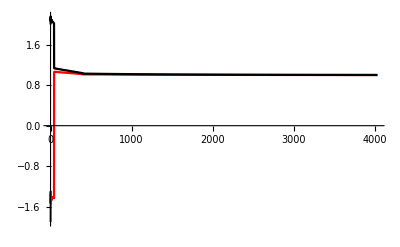

```mathematica
(* Die Iterationsverlauf von x1 und x2 *)
ListLinePlot[Transpose[X],PlotStyle->{Red,Black},PlotRange->All]
```

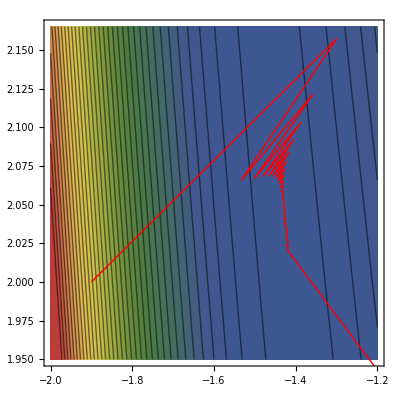

```mathematica
(* Die Iterierten x^0 bis x^42 *)  
ContourPlot[f[{x1,x2}],{x1,-2,-1.2},{x2,1.95,2.165},Epilog->{Red,PointSize[0.0015],Map[Point,X],Line[X]},  ColorFunction->"DarkRainbow", Contours->35]
```

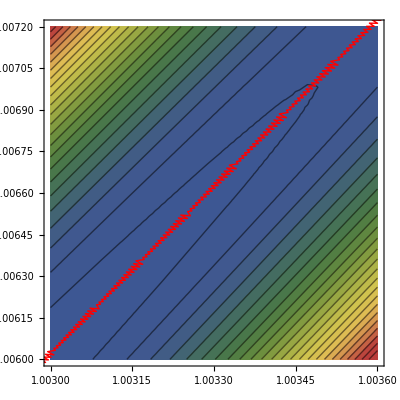

```mathematica
(* Iterationsverlauf kurz vor Minimum (1,1) *)
ContourPlot[f[{x1,x2}],{x1,1.003,1.0036},{x2,1.006,1.0072},Epilog->{Red,PointSize[0.0015],Map[Point,X],Line[X]},  ColorFunction->"DarkRainbow", Contours->25]
```

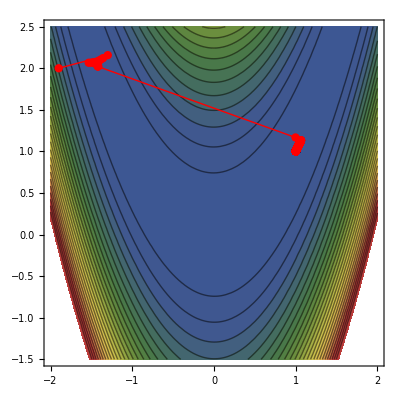

```mathematica
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-1.5,2.5},Epilog->{Red,PointSize[0.015],Map[Point,X],Line[X]},  ColorFunction->"DarkRainbow",  Contours->25]
```

```mathematica
G1=Plot3D[f[{x1,x2}],{x1,-2,2},{x2,-1.5,2.5}, ColorFunction->"DarkRainbow", Boxed->False, AxesLabel->Automatic, Mesh->None];
G2=Graphics3D[{PointSize[0.02],Red,Point[Table[{X[[i,1]],X[[i,2]],f[{X[[i,1]],X[[i,2]]}]},{i,1,Length[X]}]]}];
G3=Graphics3D[{Red,Line[Table[{X[[i,1]],X[[i,2]],f[{X[[i,1]],X[[i,2]]}]},{i,1,Length[X]}]]}];
Show[G1,G2,G3]
```

-Graphics3D-

### Konvergenzgeschwindigkeit bei versch. ϵ-Werte

#### ϵ = 10^(-2), 1150 Iterationen

```mathematica
Norm[{1.007844634602773,1.0157662290974787}-{1.,1.}]
```

0.01761

#### ϵ = 10^(-3), 4031 Iterationen

```mathematica
Norm[{1.0007809416256455,1.0015671709533085}-{1.,1.}]
```

0.00175097

#### ϵ = 10^(-4), 6884 Iterationen

```mathematica
Norm[{1.0000774985140735,1.0001554737613876}-{1.,1.}]
```

0.000173718

#### ϵ = 10^(-5), 9705 Iterationen

```mathematica
Norm[{1.0000078593615962,1.0000157657353972}-{1.,1.}]
```

0.0000176161

#### ϵ = 10^(-6), 12545 Iterationen

```mathematica
Norm[{1.0000007851861243,1.0000015751028364}-{1.,1.}]
```

1.75996×10^-6

#### ϵ = 10^(-7), 15385 Iterationen

```mathematica
Norm[{1.0000000784444656,1.0000001573614579}-{1.,1.}]
```

1.7583×10^-7

#### ϵ = 10^(-8), 18225 Iterationen

```mathematica
Norm[{1.000000007837046,1.0000000157212594}-{1.,1.}]
```

1.75664×10^-8